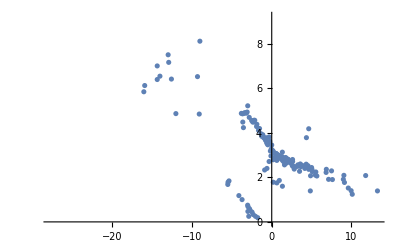

```mathematica
data = Import["Documents/Github/POE/PoeLab2/POE Lab 2 Data.csv"][[1]];
data = ArrayReshape[data, {Length[data]/3,3}];
MatrixPlot[data];
data[[All, 2;;3]];

ListPlot[data[[All, 2;;3]]]
```